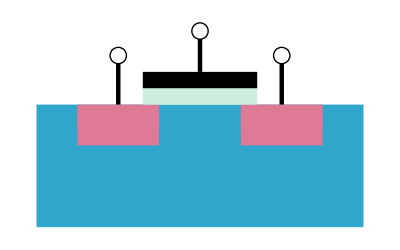

```mathematica
Graphics[

transistor={
Style[Rectangle[{0,0},{2,0.75},RoundingRadius->0.1],RGBColor[0.19,0.65,0.8]],Style[Rectangle[{0.25,0.5},{0.75,0.75},RoundingRadius->0.1],RGBColor[0.87,0.48,0.59]],
Style[Rectangle[{1.25,0.5},{1.75,0.75},RoundingRadius->0.1],RGBColor[0.87,0.48,0.59]],
Style[Rectangle[{1.25,0.6},{1.75,0.745}],RGBColor[0.87,0.48,0.59]],
Style[Rectangle[{0.25,0.6},{0.75,0.745}],RGBColor[0.87,0.48,0.59]],
Style[Rectangle[{0.65,0.75},{1.35,0.85}],RGBColor[0.8,0.93,0.86]],
Style[Rectangle[{0.65,0.85},{1.35,0.95}]],
Style[Line[{{0.5,0.75},{0.5,1}}],Thickness[0.008]],
Style[Line[{{1.5,0.75},{1.5,1}}],Thickness[0.008]],
Style[Line[{{1,0.95},{1,1.15}}],Thickness[0.008]],
Circle[{1.5,1.05},0.05],
Circle[{0.5,1.05},0.05],
Circle[{1.,1.2},0.05]
}]
```

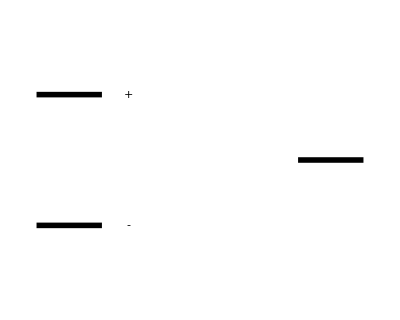

```mathematica
Graphics[opamp=
{Style[Triangle[{{0,0},{1.5,1},{0,2}}],Opacity[0],EdgeForm[{Thickness[0.01], Black}]],
Style[Text["+",{0.2,1.5}],FontSize->60],
Style[Text["-",{0.2,0.5}],FontSize->60],
Style[Line[{{-0.5,0.5},{0,0.5}}],Thickness[0.01]],
Style[Line[{{-0.5,1.5},{0,1.5}}],Thickness[0.01]],
Style[Line[{{1.5,1},{2,1}}],Thickness[0.01]]
}]
```

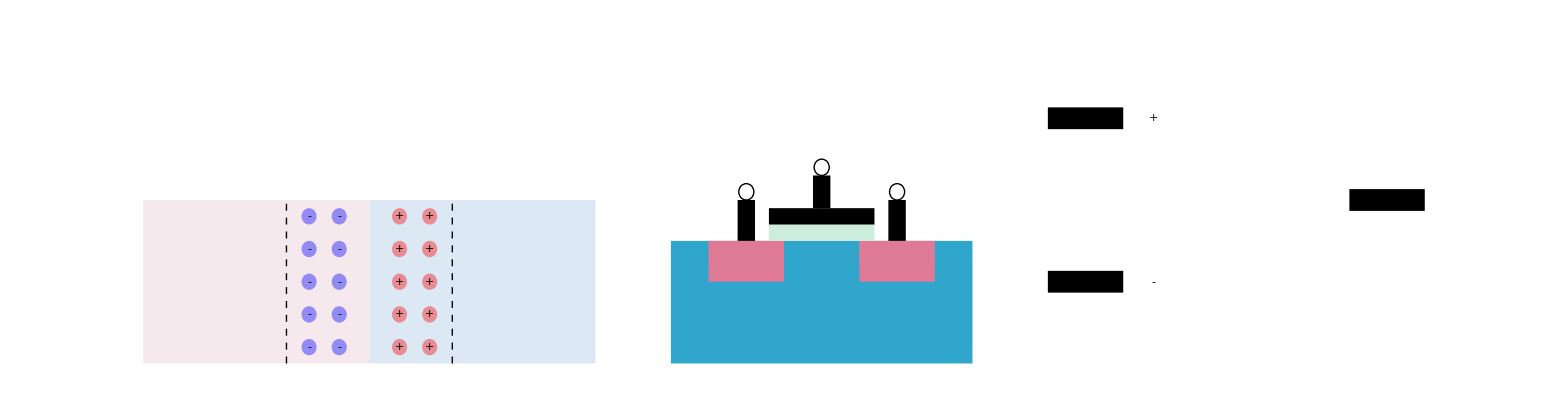

```mathematica
Graphics[{Translate[diode,{-3,0}],Translate[opamp,{3,0}],transistor},ImageSize->{1600,400}]
```

```mathematica
Graphics3D[
{
Style[Sphere[],Blue],
Style[Text["e^-"],White,FontSize->45]
},Boxed->False]
```

-Graphics3D-

```mathematica
axesYBare={Style[Arrow[{{0,0,0},{1,0,0}}],Black,Thick],
Style[Arrow[{{0,0,0},{0,1,0}}],Black,Thick],
Style[Arrow[{{0,0,0},{0,0,1}}],Black,Thick],}
```

{Arrow[{{0,0,0},{1,0,0}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{0,0,1}}],Null}

```mathematica
Graphics3D[{axesYBare,
DeleteCases[Table[If[√(i^2+j^2+k^2)≤0.85,Style[Sphere[{i,j,k},0.01],Opacity[0.2],Black],None],{i,0,1,0.05},{j,0,1,0.05},{k,0,1,0.05}]//Flatten,None]
},Boxed->False,ViewPoint->{0,0,π/2}]
```

-Graphics3D-

```mathematica
Unprotect[k];Clear[k]
```

```mathematica
DeleteCases[{1,2,None},None]
```

{1,2}

{Sphere[{0.,0.,0.},0.01],Sphere[{0.,0.,0.5},0.01],Sphere[{0.,0.,1.},0.01],Sphere[{0.,0.5,0.},0.01],Sphere[{0.,0.5,0.5},0.01],Sphere[{0.,1.,0.},0.01],Sphere[{0.5,0.,0.},0.01],Sphere[{0.5,0.,0.5},0.01],Sphere[{0.5,0.5,0.},0.01],Sphere[{0.5,0.5,0.5},0.01],Sphere[{1.,0.,0.},0.01]}

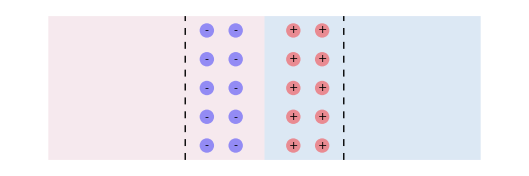

```mathematica
Graphics[
diode={Style[Rectangle[{-0.5,0},{1,1}],Opacity[0.2],RGBColor[0.84,0.58,0.68]],
Style[Rectangle[{1,0},{2.5,1}],Opacity[0.2],RGBColor[0.33,0.55,0.79]],
Table[Style[Disk[{0.8,i},0.05],Opacity[0.4],Blue],{i,0.1,0.9,0.2}],
Table[Style[Text["-",{0.8,i}],FontSize->14],{i,0.1,0.9,0.2}],
Table[Style[Disk[{0.6,i},0.05],Opacity[0.4],Blue],{i,0.1,0.9,0.2}],
Table[Style[Text["-",{0.6,i}],FontSize->14],{i,0.1,0.9,0.2}],
Table[Style[Disk[{1.2,i},0.05],Opacity[0.4],Red],{i,0.1,0.9,0.2}],
Table[Style[Text["+",{1.2,i}],FontSize->14],{i,0.1,0.9,0.2}],
Table[Style[Disk[{1.4,i},0.05],Opacity[0.4],Red],{i,0.1,0.9,0.2}],
Table[Style[Text["+",{1.4,i}],FontSize->14],{i,0.1,0.9,0.2}],
Style[Line[{{0.45,0},{0.45,1}}],Dashed],
Style[Line[{{1.55,0},{1.55,1}}],Dashed]
}]
```

```mathematica
1500/(2*30)//N
```

25.